# Bessel K NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## Definitions and derivations

```mathematica
BesselK`D[u_,α_,a_]:=(2 (1-u^2)^(-1/2+a/2) (u α)^-a BesselK[1-a,(2 √(1-u^2))/(u α)])/(π u^3 α Gamma[a])HeavisideTheta[u]
```

### derivation

```mathematica
Beckmann`D[u_,α_]:=(ⅇ^(-(-1+1/u^2)/α^2))/(α^2 π u^4)HeavisideTheta[u]
```

```mathematica
Integrate[Beckmann`D[u,α √m]PDF[GammaDistribution[a,1]][m],{m,0,Infinity},Assumptions->0<u<1&&α>0&&a>0]
```

(2 (1-u^2)^(-1/2+a/2) (u α)^-a BesselK[1-a,(2 √(1-u^2))/(u α)])/(π u^3 α Gamma[a])

```mathematica
FullSimplify[Integrate[Beckmann`D[u, α/(√2) m]PDF[ChiDistribution[2 a]][m],{m,0,Infinity},Assumptions->0<u<1&&α>0&&a>0],Assumptions->a>0&&α>0]
```

(2 (1-u^2)^(1/2 (-1+a)) (u α)^(-1-a) BesselK[-1+a,(2 √(1-u^2))/(u α)])/(π u^2 Gamma[a])

### shape invariant f(x)

```mathematica
FullSimplify[BesselK`D[u,α,a] u^4 α^2/.u->1/(√(1+x^2 α^2)),Assumptions->1-1/(√(1+x^2 α^2))>0&&x>0&&α>0&&a>0]
```

(2 x^(-1+a) BesselK[-1+a,2 x])/(π Gamma[a])

### height field normalization

```mathematica
NIntegrate[2Pi u BesselK`D[u,.6,1.6],{u,0,1}]
```

1.

### distribution of slopes

```mathematica
FullSimplify[BesselK`D[1/(√(p^2+q^2+1)),α,a](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

(2 (p^2+q^2)^(1/2 (-1+a)) α^(-1-a) BesselK[-1+a,(2 √(p^2+q^2))/α])/(π Gamma[a])

```mathematica
BesselK`P22[p_,q_,α_,a_]:=(2 (p^2+q^2)^(1/2 (-1+a)) α^(-1-a) BesselK[-1+a,(2 √(p^2+q^2))/α])/(π Gamma[a])
```

```mathematica
Integrate[BesselK`P22[p,q,α,a],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1&&a>0]
```

1

### importance sampling

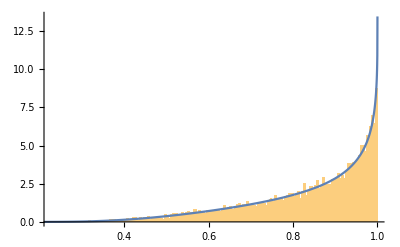

```mathematica
With[{α=.7,a=1.3},
Show[
Histogram[Table[1/(√(1-(α/(√2) RandomVariate[ChiDistribution[2 a]])^2 (Log[RandomReal[]]))),{i,Range[10000]}],200,"PDF"],
Plot[BesselK`D[u,α,a]2 Pi u,{u,0,1},PlotRange->All]
]
]
```